0.5

1.1

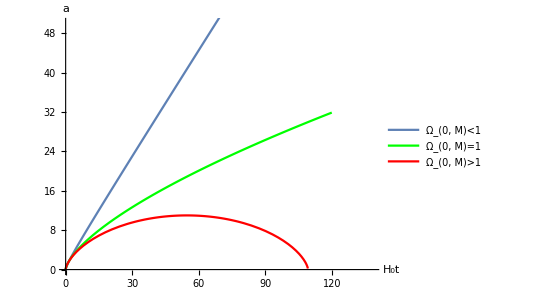

curvature_matter_universe.pdf

```mathematica
Subscript[Ω, 1]=0.5
Subscript[Ω, 2]=1.1
p1=Show[ParametricPlot[{{Subscript[Ω, 1]/(2*(1-Subscript[Ω, 1])^(3/2))*(Sinh[t]-t),Subscript[Ω, 1]/(1-Subscript[Ω, 1])*(Sinh[t/2])^2}},{t,0,6},PlotLegends->{"Ω_(0, M)<1"}],Plot[(3/2)^(2/3)t^(2/3),{t,0,120},PlotStyle->Green,PlotLegends->{"Ω_(0, M)=1"}],ParametricPlot[{{Subscript[Ω, 2]/(2*(Subscript[Ω, 2]-1)^(3/2))*(t-Sin[t]),Subscript[Ω, 2]/(Subscript[Ω, 2]-1)*(Sin[t/2])^2}},{t,0,6},PlotStyle->Red,PlotLegends->{"Ω_(0, M)>1"}],PlotRange->{0,50},AspectRatio->0.75,AxesLabel->{"H_0t",a}]
Export["curvature_matter_universe.pdf",p1]
```